## Интерполяция функции f(x)=1/(1+x^2) на равномерной сетке

Изначальная функция:

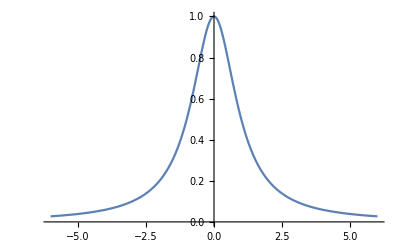

```mathematica
f[x_] = 1/(1+x^2);
Plot[f[x], {x, -6, 6}]
```

Разобьем промежуток на 4, 8, 16 интервалов:

```mathematica
data1 = N[f[Range[-6, 6,3]]]
data2 = N[f[Range[-6, 6,1.5 ]]]
data3 = N[f[Range[-6, 6,0.75 ]]]
```

{0.027027,0.1,1.,0.1,0.027027}

{0.027027,0.0470588,0.1,0.307692,1.,0.307692,0.1,0.0470588,0.027027}

{0.027027,0.0350109,0.0470588,0.06639,0.1,0.164948,0.307692,0.64,1.,0.64,0.307692,0.164948,0.1,0.06639,0.0470588,0.0350109,0.027027}

Запустим программу для q = 200:

```mathematica
res1 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

```mathematica
res2 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

```mathematica
res3 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

Построим графики:

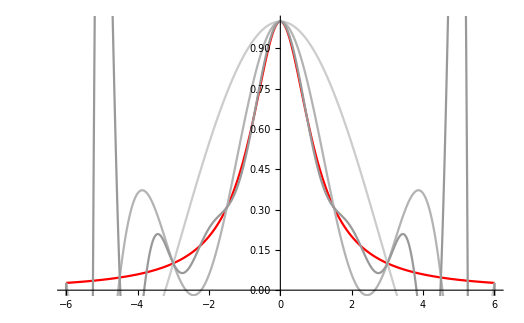

```mathematica
Show[Plot[f[x], {x, -6, 6}, ImageSize->Medium, PlotStyle->{Red}],ListLinePlot[{Transpose@{Range[-6, 6,12/800],Drop[res1, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/1600], Drop[res2, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/3200],Drop[res3, 2] //.{x_}:>x}}, PlotStyle->{RGBColor[0.8, 0.8, 0.8], RGBColor[0.7, 0.7, 0.7], RGBColor[0.6, 0.6, 0.6], RGBColor[0.9, 0.9, 0.9]}]]
```

Из графика видно, что получается бред.

## Интерполяция функции f(x)=1/(1+x^2) на Чебышевской сетке

Снова разобьем промежуток на 4, 8, 16 интервалов, на этот раз по-чебышевски:

```mathematica
a = -6;
b = 6;
cheb[k_, n_] :=(a+b)/2.0+(a-b)/2.0*Cos[(2.0*k+1.0)/(2.0*n+2.0)*Pi]
```

```mathematica
data1 = N[f[cheb[Range[0, 4, 1],4]]]
data2 = N[f[cheb[Range[0, 8, 1],8]]]
data3 = N[f[cheb[Range[0, 16, 1],16]]]
```

{0.0297953,0.0744175,1.,0.0744175,0.0297953}

{0.0278439,0.0357143,0.0629948,0.191894,1.,0.191894,0.0629948,0.0357143,0.0278439}

{0.0272528,0.0291512,0.0335037,0.0417957,0.0576729,0.091102,0.175505,0.451365,1.,0.451365,0.175505,0.091102,0.0576729,0.0417957,0.0335037,0.0291512,0.0272528}

Запустим программу для q = 200:

```mathematica
res1 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

```mathematica
res2 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

```mathematica
res3 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

Построим графики:

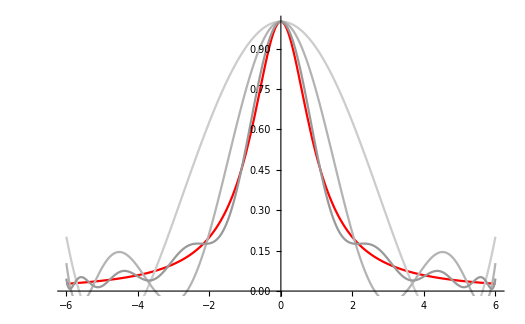

```mathematica
Show[Plot[f[x], {x, -6, 6}, ImageSize->Medium, PlotStyle->{Red}],ListLinePlot[{Transpose@{Range[-6, 6,12/800],Drop[res1, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/1600], Drop[res2, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/3200],Drop[res3, 2] //.{x_}:>x}}, PlotStyle->{RGBColor[0.8, 0.8, 0.8], RGBColor[0.7, 0.7, 0.7], RGBColor[0.6, 0.6, 0.6], RGBColor[0.9, 0.9, 0.9]}]]
```

Это уже куда лучше.

## Интерполяция константной функции на равномерной сетке

Возьмем следующие данные:

```mathematica
data1 = {0, 0, 1, 0, 0};
data2 = {0, 0, 0, 0, 1, 0, 0, 0, 0};
data3 ={0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0};
```

Запустим программу для q = 200:

```mathematica
res1 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

```mathematica
res2 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

```mathematica
res3 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_uniform.dat"];
```

Построим графики:

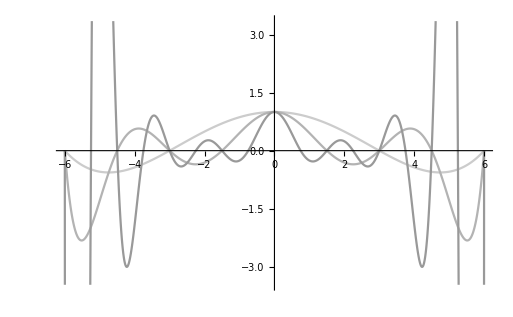

```mathematica
Show[ListLinePlot[{Transpose@{Range[-6, 6,12/800],Drop[res1, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/1600], Drop[res2, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/3200],Drop[res3, 2] //.{x_}:>x}}, PlotStyle->{RGBColor[0.8, 0.8, 0.8], RGBColor[0.7, 0.7, 0.7], RGBColor[0.6, 0.6, 0.6], RGBColor[0.9, 0.9, 0.9]}]]
```

Плохо получилось.

## Интерполяция константной функции на Чебышевской сетке

По аналогичным данным запустим программу для q = 200:

```mathematica
res1 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

```mathematica
res2 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

```mathematica
res3 = Import["/Users/severin/Desktop/Практикум/numerical-task-2.1/res_chebyshev.dat"];
```

Построим графики:

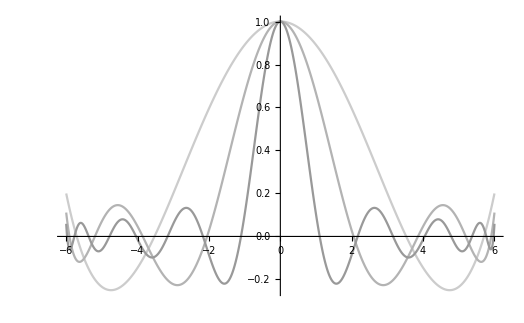

```mathematica
Show[ListLinePlot[{Transpose@{Range[-6, 6,12/800],Drop[res1, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/1600], Drop[res2, 2] //.{x_}:>x}, Transpose@{Range[-6, 6,12/3200],Drop[res3, 2] //.{x_}:>x}}, PlotStyle->{RGBColor[0.8, 0.8, 0.8], RGBColor[0.7, 0.7, 0.7], RGBColor[0.6, 0.6, 0.6], RGBColor[0.9, 0.9, 0.9]}]]
```

Снова лучше.

## Вывод — интерполяция по Чебышеву точнее, хоть и требует 5 вложенных циклов вместо 3.